# All the initialization

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Import["../../neatphos.m"];
```

```mathematica
ResourceFunction["KernelStatusGrid"]
CreatePalette[{{"[◼]", "KernelStatusGrid"}}[]]
```

[◼] | KernelStatusGrid

s3zzf_shm32FrontEndObject[LinkObject["s3zzf_shm", 3, 1]]32Untitled-4

```mathematica
quantkeys={"ndeparams","ndeevs","ndenefs","onc","fox","foy","alphax","alphay","afax","afay"};
envkeys={"fs","ss","hs","he"};
potkeys={"rk","c"};
muinds=Table[i,{i,4}];
mukeys=Table[ToString@StringForm["mu`1`",i],{i,4}];
dinds=Table[i,{i,0,9}];
dukeys=Table[ToString@StringForm["d`1`",i],{i,0,9}];
envleg=<|"fs"->"Freestanding ","ss"->"SiO2 Supported ","hs"->"h-BN Supported ","he"->"h-BN Encapsulated"|>;
potleg=<|"rk"->"RK, ","c"->"Coulomb, "|>;
muleg=<|"mu1"->TraditionalForm["μ_1, "],"mu2"->TraditionalForm["μ_2, "],"mu3"->TraditionalForm["μ_3, "],"mu4"->TraditionalForm["μ_4, "]|>;
dleg=<|Flatten[{"d0"->"Direct ",Table[tssf["d`1`",i]->tssf["N = `1`, D = `2`",i,rightd[i]],{i,1,9}]}]|>;
quantleg=<|"ndeevs"->"EVs","ndenefs"->"EFs","onc"->"Orthonormality","fox"->"Osc Str x","foy"->"Osc Str y","alphax"->"alpha x","alphay"->"alpha y","afax"->"abs fac x","afay"->"abs fac y"|>;
xleg=<|"i1"->"n","d0"->TraditionalForm["N_(h - BN)"]|>;
ixax=<|Table[tssf["i`1`",i]->i,{i,12}]|>;
bgclr[expr_,clr_RGBColor]:=Framed[expr,FrameStyle->None,Background->clr]
bgclr[clr_RGBColor,expr_]:=Framed[expr,FrameStyle->None,Background->clr]
combopltexp[filename_,plt_]:={
Export[figdir<>"comb-"<>filename<>".eps",ccol[{plt[[2,1]],plt[[1]]}],"EPS","PreviewFormat"->"TIFF"],
Export[figdir<>"plt-"<>filename<>".eps",plt[[1]],"EPS","PreviewFormat"->"TIFF"],
Export[figdir<>"leg-"<>filename<>".eps",plt[[2,1]],"EPS","PreviewFormat"->"TIFF"]
}
showandexp[filename_,plt_]:=TableForm@{
bgclr[{combopltexp[filename,plt]},LightRed],
{plt[[2,1]],plt[[1]]}//ccol
}
framegrid[data_]:=Grid[data,Frame->All]
noemptyassoc=(Select[#,UnsameQ[#,<||>]&]&);
selchop[chp_:(10^-4)]:=Select[(#>chp)&]
```

## Import the Data

### Batch import of data

```mathematica
AbsoluteTiming[allres=Association@Table[env->Association@Table[pot->Association@Table[ToString@StringForm["mu`1`",muind]->Association@Table[ToString@StringForm["d`1`",dind]->
Module[
{
pars,evs,efs,onc,fox,foy,alphax,alphay,afax,afay,nmax
},
{pars,evs,efs,onc,fox,foy,alphax,alphay,afax,afay}=Table[Import[ToString@StringForm["`1`_`2`_`3`_mu`4`_d`5`.m",quantity,pot,env,muind,dind]],{quantity,quantkeys}];
nmax=Length[evs];
(*
Actually, don't make the formatted tables here.
What would be better is making a table function that can take an arbitrary nested association and format a table from that.
which sounds pretttttttyyyyyy tricky...
--- But for now I can make associations for the lists of data I get from Import
*)
<|
"ndeparams"->pars,
"ndeevs"-><|Table[ToString@StringForm["i`1`",i]->UnitConvert[Quantity[evs[[i]],"Hartrees"],"Millielectronvolts"],{i,nmax}]|>,
"ndenefs"-><|Table[ToString@StringForm["i`1`",i]->efs[[i]],{i,nmax}]|>,
(* Make **both** a ragged array and a square array.... because reasons *)
"onc"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->onc[[i,j-i+1]],
{j,i,12}
]|>,
{i,12}
]|>,
"oncsq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[onc,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"fox"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->fox[[i,j-i+1]],
{j,i,12}
]|>,
{i,12}
]|>,
"foxsq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[fox,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"foy"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->foy[[i,j-i+1]],
{j,i,12}
]|>,
{i,12}
]|>,
"foysq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[foy,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"alphax"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->If[i==j,0,alphax[[i,j-i+1]]],
{j,i,11}
]|>,
{i,12}
]|>,
"alphaxsq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[alphax,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"alphay"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->If[i==j,0,alphay[[i,j-i+1]]],
{j,i,11}
]|>,
{i,12}
]|>,
"alphaysq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[alphay,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"afax"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->If[i==j,0,afax[[i,j-i+1]]],
{j,i,11}
]|>,
{i,12}
]|>,
"afaxsq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[afax,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"afay"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->If[i==j,0,afay[[i,j-i+1]]],
{j,i,11}
]|>,
{i,12}
]|>,
"afaysq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[afay,{12,12},0])
|>
],
{dind,If[env=="he",dinds,{0}]}],
{muind,muinds}],
{pot,If[env=="he",potkeys,{"rk"}]}],
{env,envkeys}];]
dsar=Dataset[allres];
```

{170.733,Null}

### Helper functions for Dataset

#### Flatten association and merge keys

```mathematica
flatassmerge=Association[KeyValueMap[
Module[{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]&]];
```

#### Map keys to x-values

```mathematica
keytox[key_]:=<|
Flatten[{
Table[tssf["i`1`",i]->i,{i,12}],
Table[tssf["j`1`",i]->i,{i,12}],
Table[tssf["d`1`",d]->rightd[d-1],{d,0,9}]
}]|>[key]
```

#### Define the x-y pair maker:

```mathematica
xymaker[data_]:=Map[
KeyValueMap[{keytox[#1],Abs@QuantityMagnitude[#2]}&],
data,
{-3}
]
```

#### Define the key-to-legend formatter

```mathematica
keytoleg[key_]:=<|Flatten[{
"fs"->"Freestanding","ss"->"SiO_2 Subst.","hs"->"h-BN Subst.","he"->"h-BN Encap.",
"rk"->"RK","c"->"Coulomb",
Table[tssf["mu`1`",i]->tssf["μ_(`1`)",i],{i,4}],
"d0"->"Direct",Table[tssf["d`1`",d]->tssf["Indirect (N = `1`, D = `2` Å)",d,rightd[d-1]],{d,1,9}]
}]|>[key]
```

#### Function that takes a list of ‘keytoleg’ outputs and StringRiffles them

```mathematica
makeleg[strlist_]:=TraditionalForm[StringRiffle[keytoleg/@strlist,"; "]]
```

#### Find nested depth of Association

```mathematica
assocdepth[ass_]:=Module[
{
hed=Part[
ass,
##
]&@@{0},
headpart={0},
assdepth=0
},
While[hed==Association,
assdepth+=1;
headpart=Prepend[headpart,1];
hed=Part[
ass,
##
]&@@headpart;
];
assdepth
]
```

#### Take xy-data and extract the nested associations

```mathematica
datncap[data_]:=Module[
{
xydata=Normal[data[xymaker]],
asdep,dat,leg
},
asdep=assocdepth[xydata];
{dat,leg}=Flatten[
Map[
KeyValueMap[#2&],
MapIndexed[
{#1,#2}&,
xydata,
{asdep}
],
{0,asdep-1}
],
asdep-1
]//Transpose;
{dat,leg[[;;,;;,1]]}
]
```

#### Make a Plot from the data

```mathematica
Clear[makellp]
makellp[dataset_,plopts:OptionsPattern[]]:=Module[
{
data,legs
},
{data,legs}=datncap[dataset];
ListLinePlot[
data,
ImageSize->{1600,900},PlotTheme->"Detailed",PlotRange->All,PlotMarkers->{Automatic,20},
Evaluate@FilterRules[{plopts},Options[ListLinePlot]],
PlotLegends->Placed[LineLegend[Automatic,makeleg/@legs,LabelStyle->Directive[16,Black,FontFamily->"Arial"],LegendFunction->"Panel",LegendLayout->{"Column",4}],Above]
]
]
```

#### Define some standard markers and line styles for common data sets

Get a permanent set of dashed colored lines from random generation

```mathematica
Riffle[
{RandomSample[ColorData[99,"ColorList"],12]},
{Table[
Dashing[RandomSample[dshng,First@RandomSample[dshnum,1]]],
{12}
]}
]
```

{{RGBColor[0.65, 0., 0.],RGBColor[0.212151, 0.39271, 0.8],RGBColor[0.659814, 0.212037, 0.300311],RGBColor[0.111025, 0.56, 0.418696],RGBColor[0.752461, 0.362306, 0.125339],RGBColor[0.7055434835026511, 0.5895048315002945, 0.],RGBColor[0.0504678, 0.526626, 0.627561],RGBColor[0.435888, 0.259065, 0.71028],RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516],RGBColor[0.784922, 0.524612, 0.0407096],RGBColor[0.515278, 0.224, 0.530342],RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278]},{Dashing[{Large,Tiny,Small}],Dashing[{Large,Medium,Tiny}],Dashing[{Tiny}],Dashing[{Tiny,Small}],Dashing[{Large}],Dashing[{Large}],Dashing[{Large,Tiny,Medium}],Dashing[{Large,Small,Tiny,Medium}],Dashing[{Large}],Dashing[{Tiny,Small}],Dashing[{Small,Medium,Large}],Dashing[{Large,Small}]}}

```mathematica
%//InputForm
```

{{RGBColor[0.65, 0., 0.], RGBColor[0.212151, 0.39271, 0.8], RGBColor[0.659814, 0.212037, 0.300311], RGBColor[0.111025, 0.56, 0.418696], RGBColor[0.752461, 0.362306, 0.125339], RGBColor[0.7055434835026511, 0.5895048315002945, 0.], RGBColor[0.0504678, 0.526626, 0.627561], 
  RGBColor[0.435888, 0.259065, 0.71028], RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516], RGBColor[0.784922, 0.524612, 0.0407096], RGBColor[0.515278, 0.224, 0.530342], RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278]}, 
 {Dashing[{Large, Tiny, Small}], Dashing[{Large, Medium, Tiny}], Dashing[{Tiny}], Dashing[{Tiny, Small}], Dashing[{Large}], Dashing[{Large}], Dashing[{Large, Tiny, Medium}], Dashing[{Large, Small, Tiny, Medium}], Dashing[{Large}], Dashing[{Tiny, Small}], 
  Dashing[{Small, Medium, Large}], Dashing[{Large, Small}]}}

```mathematica
{
RandomSample[Darker[ColorData[54,"ColorList"][[;;12]],0.15],12],
Table[
Dashing[RandomSample[dshng,First@RandomSample[dshnum,1]]],
{12}
]
}//Transpose//TableForm
```

RGBColor[0.32206245, 0.7423084, 0.6694166500000001] | Dashing[{Tiny,Small,Large,Medium}]
RGBColor[0.6150583, 0.67238655, 0.8192351] | Dashing[{Small,Medium}]
RGBColor[0.68559045, 0.32758745, 0.6483528000000001] | Dashing[{Small,Large}]
RGBColor[0.23214010000000002, 0.46154320000000004, 0.42124554999999997] | Dashing[{Medium,Tiny,Small}]
RGBColor[0.85, 0.44981829999999995, 0.27609615000000004] | Dashing[{Tiny}]
RGBColor[0.5939944500000001, 0.7423084, 0.25095995] | Dashing[{Large,Medium,Tiny,Small}]
RGBColor[0.85, 0.84861195, 0.36955875000000005] | Dashing[{Tiny,Small,Large}]
RGBColor[0.85, 0.8490276, 0.0017639455] | Dashing[{Tiny,Small}]
RGBColor[0.66538255, 0.1401684, 0.3403893] | Dashing[{Tiny}]
RGBColor[0.7423084, 0.1279114, 0.21686135] | Dashing[{Large,Medium}]
RGBColor[0.7228144999999999, 0.47463065000000004, 0.] | Dashing[{Small,Large}]
RGBColor[0.77307415, 0.5218286, 0.1735666] | Dashing[{Small,Tiny,Large}]

```mathematica
%//InputForm
```

{{RGBColor[0.32206245, 0.7423084, 0.6694166500000001], Dashing[{Tiny, Small, Large, Medium}]}, {RGBColor[0.6150583, 0.67238655, 0.8192351], Dashing[{Small, Medium}]}, {RGBColor[0.68559045, 0.32758745, 0.6483528000000001], Dashing[{Small, Large}]}, 
 {RGBColor[0.23214010000000002, 0.46154320000000004, 0.42124554999999997], Dashing[{Medium, Tiny, Small}]}, {RGBColor[0.85, 0.44981829999999995, 0.27609615000000004], Dashing[{Tiny}]}, {RGBColor[0.5939944500000001, 0.7423084, 0.25095995], Dashing[{Large, Medium, Tiny, Small}]}, 
 {RGBColor[0.85, 0.84861195, 0.36955875000000005], Dashing[{Tiny, Small, Large}]}, {RGBColor[0.85, 0.8490276, 0.0017639455], Dashing[{Tiny, Small}]}, {RGBColor[0.66538255, 0.1401684, 0.3403893], Dashing[{Tiny}]}, {RGBColor[0.7423084, 0.1279114, 0.21686135], Dashing[{Large, Medium}]}, 
 {RGBColor[0.7228144999999999, 0.47463065000000004, 0.], Dashing[{Small, Large}]}, {RGBColor[0.77307415, 0.5218286, 0.1735666], Dashing[{Small, Tiny, Large}]}}

```mathematica
fullmarks4={"■","●","◆","▮"};
emmarks4={"□","○","◇","▯"};
cols4={Red,Blue,Purple,Orange};
ccol[figs_]:=Column[figs,Center]
figdir="../../figures/";
nvv[assoc_]:=Values[Values[Normal[assoc]]]
randash=Transpose@{{RGBColor[0.65,0.,0.],RGBColor[0.212151,0.39271,0.8],RGBColor[1,0.212037,0.300311],RGBColor[0.111025,0.56,0.418696],RGBColor[0.752461,0.362306,0.125339],RGBColor[0.7055434835026511,0.5895048315002945,0.],RGBColor[0.0504678,0.526626,0.627561],RGBColor[0.435888,0.259065,0.71028],RGBColor[0.4078757751993936,0.27540579780035374,0.780310562001516],RGBColor[0.784922,0.524612,0.0407096],RGBColor[0.515278,0.224,0.530342],RGBColor[0.12461179749810647,0.4603105620015149,0.7095341569977278]},{Dashing[{Large,Tiny,Small}],Dashing[{Large,Medium,Tiny}],Dashing[{Tiny}],Dashing[{Tiny,Small}],Dashing[{Large}],Dashing[{Large}],Dashing[{Large,Tiny,Medium}],Dashing[{Large,Small,Tiny,Medium}],Dashing[{Large}],Dashing[{Tiny,Small}],Dashing[{Small,Medium,Large}],Dashing[{Large,Small}]}}
```

{{RGBColor[0.65, 0., 0.],Dashing[{Large,Tiny,Small}]},{RGBColor[0.212151, 0.39271, 0.8],Dashing[{Large,Medium,Tiny}]},{RGBColor[1, 0.212037, 0.300311],Dashing[{Tiny}]},{RGBColor[0.111025, 0.56, 0.418696],Dashing[{Tiny,Small}]},{RGBColor[0.752461, 0.362306, 0.125339],Dashing[{Large}]},{RGBColor[0.7055434835026511, 0.5895048315002945, 0.],Dashing[{Large}]},{RGBColor[0.0504678, 0.526626, 0.627561],Dashing[{Large,Tiny,Medium}]},{RGBColor[0.435888, 0.259065, 0.71028],Dashing[{Large,Small,Tiny,Medium}]},{RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516],Dashing[{Large}]},{RGBColor[0.784922, 0.524612, 0.0407096],Dashing[{Tiny,Small}]},{RGBColor[0.515278, 0.224, 0.530342],Dashing[{Small,Medium,Large}]},{RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278],Dashing[{Large,Small}]}}

# All the data

## Direct

## EVs

## EFs

## E_tr

## f_0

## α

## 𝒜

## Indirect

# Experimenting and such

## Pulling data from different quantities into one graph

### More focused

First, for each μ, transform the “i_n” to "(n_x,n_y)".
Then, make two assoc’s, one for increasing n_x and one for increasing n_y.
Then make intervals across the μ’s for the n_x and n_y assocs.
Then on one plot we’ll have two sets of data with intervals, for n_x and n_y.

#### Map the i_n to (n_x,n_y) for each μ_i

```mathematica
i2nxy=<|"mu1"-><|
"i1"->"{0,0}",
"i2"->"{0,1}",
"i3"->"{0,2}",
"i4"->"{0,3}",
"i5"->"{0,4}",
"i6"->"{1,0}",
"i7"->"{0,5}",
"i8"->"{0,6}",
"i9"->"{1,1}",
"i10"->"{0,7}",
"i11"->"{2,1}",
"i12"->"{0,8}"
|>,
"mu2"-><|
"i1"->"{0,0}",
"i2"->"{0,1}",
"i3"->"{0,2}",
"i4"->"{0,3}",
"i5"->"{0,4}",
"i6"->"{1,0}",
"i7"->"{0,5}",
"i8"->"{0,6}",
"i9"->"{1,1}",
"i10"->"{0,7}",
"i11"->"{2,1}",
"i12"->"{0,8}"
|>,
"mu3"-><|
"i1"->"{0,0}",
"i2"->"{0,1}",
"i3"->"{0,2}",
"i4"->"{1,0}",
"i5"->"{0,3}",
"i6"->"{0,4}",
"i7"->"{1,1}",
"i8"->"{0,5}",
"i9"->"{0,6}",
"i10"->"{2,1}",
"i11"->"{0,7}",
"i12"->"{0,8}"
|>,
"mu4"-><|
"i1"->"{0,0}",
"i2"->"{0,1}",
"i3"->"{0,2}",
"i4"->"{0,3}",
"i5"->"{1,0}",
"i6"->"{0,4}",
"i7"->"{0,5}",
"i8"->"{1,1}",
"i9"->"{0,6}",
"i10"->"{2,1}",
"i11"->"{0,7}",
"i12"->"{0,8}"
|>|>;
```

```mathematica
i2nxy//Transpose//Dataset
```

Dataset[<>]

```mathematica
|
```

#### Figure out how to use it...

```mathematica
muievs=dsar["he","rk",All,"d0","ndeevs"]
```

Dataset[<>]

```mathematica
i2nxy[muievs]
muievs[KeyMap[f]]
```

Missing[KeyAbsent,Dataset[<>]]

Dataset[<>]

```mathematica
muievs[KeyMap[f]/*Values/*Map[KeyMap[g]]]//Normal
```

{<|g[i1]→-187.945 meV,g[i2]→-78.6243 meV,g[i3]→-53.8285 meV,g[i4]→-35.6655 meV,g[i5]→-27.8798 meV,g[i6]→-24.7921 meV,g[i7]→-20.8681 meV,g[i8]→-17.3962 meV,g[i9]→-15.7331 meV,g[i10]→-13.4945 meV,g[i11]→-12.2242 meV,g[i12]→-11.9369 meV|>,<|g[i1]→-188.952 meV,g[i2]→-77.1738 meV,g[i3]→-52.6492 meV,g[i4]→-34.5349 meV,g[i5]→-26.9608 meV,g[i6]→-25.7621 meV,g[i7]→-20.06 meV,g[i8]→-16.68 meV,g[i9]→-16.0407 meV,g[i10]→-12.8972 meV,g[i11]→-12.3978 meV,g[i12]→-11.986 meV|>,<|g[i1]→-199.515 meV,g[i2]→-74.3196 meV,g[i3]→-50.3129 meV,g[i4]→-31.9724 meV,g[i5]→-31.6225 meV,g[i6]→-24.6973 meV,g[i7]→-18.3087 meV,g[i8]→-17.8125 meV,g[i9]→-15.2383 meV,g[i10]→-13.9915 meV,g[i11]→-13.905 meV,g[i12]→-11.2174 meV|>,<|g[i1]→-204.666 meV,g[i2]→-84.604 meV,g[i3]→-57.7771 meV,g[i4]→-37.9366 meV,g[i5]→-30.0635 meV,g[i6]→-29.6125 meV,g[i7]→-21.9998 meV,g[i8]→-18.6052 meV,g[i9]→-18.3629 meV,g[i10]→-14.3328 meV,g[i11]→-14.1592 meV,g[i12]→-13.9545 meV|>}

```mathematica
KeyValueMap[
Module[{muky=#1,inass=#2},
{
Map[muky<>#&,Keys[inass]],
Values[inass]
}
]&][i2nxy]
Normal@muievs[
KeyValueMap[
Module[{muky=#1,inass=#2},
{
Map[muky<>#&,Keys[inass]],
Values[inass]
}
]&]
]
```

{{{mu1i1,mu1i2,mu1i3,mu1i4,mu1i5,mu1i6,mu1i7,mu1i8,mu1i9,mu1i10,mu1i11,mu1i12},{{0,0},{0,1},{0,2},{0,3},{0,4},{1,0},{0,5},{0,6},{1,1},{0,7},{2,1},{0,8}}},{{mu2i1,mu2i2,mu2i3,mu2i4,mu2i5,mu2i6,mu2i7,mu2i8,mu2i9,mu2i10,mu2i11,mu2i12},{{0,0},{0,1},{0,2},{0,3},{0,4},{1,0},{0,5},{0,6},{1,1},{0,7},{2,1},{0,8}}},{{mu3i1,mu3i2,mu3i3,mu3i4,mu3i5,mu3i6,mu3i7,mu3i8,mu3i9,mu3i10,mu3i11,mu3i12},{{0,0},{0,1},{0,2},{0,3},{0,4},{1,0},{0,5},{0,6},{1,1},{0,7},{2,1},{0,8}}},{{mu4i1,mu4i2,mu4i3,mu4i4,mu4i5,mu4i6,mu4i7,mu4i8,mu4i9,mu4i10,mu4i11,mu4i12},{{0,0},{0,1},{0,2},{0,3},{0,4},{1,0},{0,5},{0,6},{1,1},{0,7},{2,1},{0,8}}}}

{{{mu1i1,mu1i2,mu1i3,mu1i4,mu1i5,mu1i6,mu1i7,mu1i8,mu1i9,mu1i10,mu1i11,mu1i12},{-187.945 meV,-78.6243 meV,-53.8285 meV,-35.6655 meV,-27.8798 meV,-24.7921 meV,-20.8681 meV,-17.3962 meV,-15.7331 meV,-13.4945 meV,-12.2242 meV,-11.9369 meV}},{{mu2i1,mu2i2,mu2i3,mu2i4,mu2i5,mu2i6,mu2i7,mu2i8,mu2i9,mu2i10,mu2i11,mu2i12},{-188.952 meV,-77.1738 meV,-52.6492 meV,-34.5349 meV,-26.9608 meV,-25.7621 meV,-20.06 meV,-16.68 meV,-16.0407 meV,-12.8972 meV,-12.3978 meV,-11.986 meV}},{{mu3i1,mu3i2,mu3i3,mu3i4,mu3i5,mu3i6,mu3i7,mu3i8,mu3i9,mu3i10,mu3i11,mu3i12},{-199.515 meV,-74.3196 meV,-50.3129 meV,-31.9724 meV,-31.6225 meV,-24.6973 meV,-18.3087 meV,-17.8125 meV,-15.2383 meV,-13.9915 meV,-13.905 meV,-11.2174 meV}},{{mu4i1,mu4i2,mu4i3,mu4i4,mu4i5,mu4i6,mu4i7,mu4i8,mu4i9,mu4i10,mu4i11,mu4i12},{-204.666 meV,-84.604 meV,-57.7771 meV,-37.9366 meV,-30.0635 meV,-29.6125 meV,-21.9998 meV,-18.6052 meV,-18.3629 meV,-14.3328 meV,-14.1592 meV,-13.9545 meV}}}

```mathematica
LightCyan~bgclr~(mui2xy=Association@KeyValueMap[
Module[{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]&][i2nxy])
LightGreen~bgclr~(mui2evs=muievs[
KeyValueMap[
Module[{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]&]
])
```

<|mu1i1→{0,0},mu1i2→{0,1},mu1i3→{0,2},mu1i4→{0,3},mu1i5→{0,4},mu1i6→{1,0},mu1i7→{0,5},mu1i8→{0,6},mu1i9→{1,1},mu1i10→{0,7},mu1i11→{2,1},mu1i12→{0,8},mu2i1→{0,0},mu2i2→{0,1},mu2i3→{0,2},mu2i4→{0,3},mu2i5→{0,4},mu2i6→{1,0},mu2i7→{0,5},mu2i8→{0,6},mu2i9→{1,1},mu2i10→{0,7},mu2i11→{2,1},mu2i12→{0,8},mu3i1→{0,0},mu3i2→{0,1},mu3i3→{0,2},mu3i4→{0,3},mu3i5→{0,4},mu3i6→{1,0},mu3i7→{0,5},mu3i8→{0,6},mu3i9→{1,1},mu3i10→{0,7},mu3i11→{2,1},mu3i12→{0,8},mu4i1→{0,0},mu4i2→{0,1},mu4i3→{0,2},mu4i4→{0,3},mu4i5→{0,4},mu4i6→{1,0},mu4i7→{0,5},mu4i8→{0,6},mu4i9→{1,1},mu4i10→{0,7},mu4i11→{2,1},mu4i12→{0,8}|>

Dataset[<>]

```mathematica
Normal@mui2evs[All,KeyMap[mui2xy]]
```

{<|{0,0}→-187.945 meV,{0,1}→-78.6243 meV,{0,2}→-53.8285 meV,{0,3}→-35.6655 meV,{0,4}→-27.8798 meV,{1,0}→-24.7921 meV,{0,5}→-20.8681 meV,{0,6}→-17.3962 meV,{1,1}→-15.7331 meV,{0,7}→-13.4945 meV,{2,1}→-12.2242 meV,{0,8}→-11.9369 meV|>,<|{0,0}→-188.952 meV,{0,1}→-77.1738 meV,{0,2}→-52.6492 meV,{0,3}→-34.5349 meV,{0,4}→-26.9608 meV,{1,0}→-25.7621 meV,{0,5}→-20.06 meV,{0,6}→-16.68 meV,{1,1}→-16.0407 meV,{0,7}→-12.8972 meV,{2,1}→-12.3978 meV,{0,8}→-11.986 meV|>,<|{0,0}→-199.515 meV,{0,1}→-74.3196 meV,{0,2}→-50.3129 meV,{0,3}→-31.9724 meV,{0,4}→-31.6225 meV,{1,0}→-24.6973 meV,{0,5}→-18.3087 meV,{0,6}→-17.8125 meV,{1,1}→-15.2383 meV,{0,7}→-13.9915 meV,{2,1}→-13.905 meV,{0,8}→-11.2174 meV|>,<|{0,0}→-204.666 meV,{0,1}→-84.604 meV,{0,2}→-57.7771 meV,{0,3}→-37.9366 meV,{0,4}→-30.0635 meV,{1,0}→-29.6125 meV,{0,5}→-21.9998 meV,{0,6}→-18.6052 meV,{1,1}→-18.3629 meV,{0,7}→-14.3328 meV,{2,1}→-14.1592 meV,{0,8}→-13.9545 meV|>}

#### The above looks great, now put it together

```mathematica
Normal@dsar["he","rk",All,"d0","ndeevs"][
Association[KeyValueMap[
Module[{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]&]]
](*[All,KeyMap[Association@KeyValueMap[
Module[{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]&][i2nxy]]]*)
```

<|mu1i1→-187.945 meV,mu1i2→-78.6243 meV,mu1i3→-53.8285 meV,mu1i4→-35.6655 meV,mu1i5→-27.8798 meV,mu1i6→-24.7921 meV,mu1i7→-20.8681 meV,mu1i8→-17.3962 meV,mu1i9→-15.7331 meV,mu1i10→-13.4945 meV,mu1i11→-12.2242 meV,mu1i12→-11.9369 meV,mu2i1→-188.952 meV,mu2i2→-77.1738 meV,mu2i3→-52.6492 meV,mu2i4→-34.5349 meV,mu2i5→-26.9608 meV,mu2i6→-25.7621 meV,mu2i7→-20.06 meV,mu2i8→-16.68 meV,mu2i9→-16.0407 meV,mu2i10→-12.8972 meV,mu2i11→-12.3978 meV,mu2i12→-11.986 meV,mu3i1→-199.515 meV,mu3i2→-74.3196 meV,mu3i3→-50.3129 meV,mu3i4→-31.9724 meV,mu3i5→-31.6225 meV,mu3i6→-24.6973 meV,mu3i7→-18.3087 meV,mu3i8→-17.8125 meV,mu3i9→-15.2383 meV,mu3i10→-13.9915 meV,mu3i11→-13.905 meV,mu3i12→-11.2174 meV,mu4i1→-204.666 meV,mu4i2→-84.604 meV,mu4i3→-57.7771 meV,mu4i4→-37.9366 meV,mu4i5→-30.0635 meV,mu4i6→-29.6125 meV,mu4i7→-21.9998 meV,mu4i8→-18.6052 meV,mu4i9→-18.3629 meV,mu4i10→-14.3328 meV,mu4i11→-14.1592 meV,mu4i12→-13.9545 meV|>

```mathematica
Normal@dsar[
"he","rk",All
/*
KeyValueMap[ (* This collapses down the outer Association Keys and merges them with the inner Assoc. Keys *)
Module[
{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]
&]
/*
(
Map[ (* Need to Map because we've effectively lost a layer of our data Association *)
KeyMap[ (* This applies the collapsed translation Assoc to the collapsed data assoc, changing the keys of the data assoc *)
Association@KeyValueMap[ (* Collapse down the translation keys for going from Subscript[i, n] to {Subscript[n, x],Subscript[n, y]} *)
Module[
{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]&,
i2nxy
]
](* Operator form of KeyMap *)
](* Operator form of Map *)
),
"d0","ndeevs"(*,QuantityMagnitude/*Abs*)
]
```

{<|{0,0}→-187.945 meV,{0,1}→-78.6243 meV,{0,2}→-53.8285 meV,{0,3}→-35.6655 meV,{0,4}→-27.8798 meV,{1,0}→-24.7921 meV,{0,5}→-20.8681 meV,{0,6}→-17.3962 meV,{1,1}→-15.7331 meV,{0,7}→-13.4945 meV,{2,1}→-12.2242 meV,{0,8}→-11.9369 meV|>,<|{0,0}→-188.952 meV,{0,1}→-77.1738 meV,{0,2}→-52.6492 meV,{0,3}→-34.5349 meV,{0,4}→-26.9608 meV,{1,0}→-25.7621 meV,{0,5}→-20.06 meV,{0,6}→-16.68 meV,{1,1}→-16.0407 meV,{0,7}→-12.8972 meV,{2,1}→-12.3978 meV,{0,8}→-11.986 meV|>,<|{0,0}→-199.515 meV,{0,1}→-74.3196 meV,{0,2}→-50.3129 meV,{0,3}→-31.9724 meV,{0,4}→-31.6225 meV,{1,0}→-24.6973 meV,{0,5}→-18.3087 meV,{0,6}→-17.8125 meV,{1,1}→-15.2383 meV,{0,7}→-13.9915 meV,{2,1}→-13.905 meV,{0,8}→-11.2174 meV|>,<|{0,0}→-204.666 meV,{0,1}→-84.604 meV,{0,2}→-57.7771 meV,{0,3}→-37.9366 meV,{0,4}→-30.0635 meV,{1,0}→-29.6125 meV,{0,5}→-21.9998 meV,{0,6}→-18.6052 meV,{1,1}→-18.3629 meV,{0,7}→-14.3328 meV,{2,1}→-14.1592 meV,{0,8}→-13.9545 meV|>}

```mathematica
Normal@dsar[
"he","rk",All
/*
KeyValueMap[ (* This collapses down the outer Association Keys and merges them with the inner Assoc. Keys *)
Module[
{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]
&]
/*
(
Map[ (* Need to Map because we've effectively lost a layer of our data Association *)
KeyMap[ (* This applies the collapsed translation Assoc to the Keys of the collapsed data assoc, changing the keys of the data assoc *)
Association@KeyValueMap[ (* Collapse down the translation keys for going from Subscript[i, n] to {Subscript[n, x],Subscript[n, y]} *)
Module[
{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]&,
i2nxy
]
](* Operator form of KeyMap *)
](* Operator form of Map *)
)
/*
(ListPlot[#,PlotTheme->"Detailed",ImageSize->Large]&),
"d0","ndeevs",QuantityMagnitude/*Abs
]
```

-Graphics-

#### Trying a different approach...

```mathematica
Normal@muievs
```

<|mu1→<|i1→-187.945 meV,i2→-78.6243 meV,i3→-53.8285 meV,i4→-35.6655 meV,i5→-27.8798 meV,i6→-24.7921 meV,i7→-20.8681 meV,i8→-17.3962 meV,i9→-15.7331 meV,i10→-13.4945 meV,i11→-12.2242 meV,i12→-11.9369 meV|>,mu2→<|i1→-188.952 meV,i2→-77.1738 meV,i3→-52.6492 meV,i4→-34.5349 meV,i5→-26.9608 meV,i6→-25.7621 meV,i7→-20.06 meV,i8→-16.68 meV,i9→-16.0407 meV,i10→-12.8972 meV,i11→-12.3978 meV,i12→-11.986 meV|>,mu3→<|i1→-199.515 meV,i2→-74.3196 meV,i3→-50.3129 meV,i4→-31.9724 meV,i5→-31.6225 meV,i6→-24.6973 meV,i7→-18.3087 meV,i8→-17.8125 meV,i9→-15.2383 meV,i10→-13.9915 meV,i11→-13.905 meV,i12→-11.2174 meV|>,mu4→<|i1→-204.666 meV,i2→-84.604 meV,i3→-57.7771 meV,i4→-37.9366 meV,i5→-30.0635 meV,i6→-29.6125 meV,i7→-21.9998 meV,i8→-18.6052 meV,i9→-18.3629 meV,i10→-14.3328 meV,i11→-14.1592 meV,i12→-13.9545 meV|>|>

```mathematica
Normal@muievs[<|"mu1"->{Keys,Values/*Keys},"mu2"->g|>]
```

<|mu1→{{mu1,mu2,mu3,mu4},{{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}}},mu2→g[<|mu1→<|i1→-187.945 meV,i2→-78.6243 meV,i3→-53.8285 meV,i4→-35.6655 meV,i5→-27.8798 meV,i6→-24.7921 meV,i7→-20.8681 meV,i8→-17.3962 meV,i9→-15.7331 meV,i10→-13.4945 meV,i11→-12.2242 meV,i12→-11.9369 meV|>,mu2→<|i1→-188.952 meV,i2→-77.1738 meV,i3→-52.6492 meV,i4→-34.5349 meV,i5→-26.9608 meV,i6→-25.7621 meV,i7→-20.06 meV,i8→-16.68 meV,i9→-16.0407 meV,i10→-12.8972 meV,i11→-12.3978 meV,i12→-11.986 meV|>,mu3→<|i1→-199.515 meV,i2→-74.3196 meV,i3→-50.3129 meV,i4→-31.9724 meV,i5→-31.6225 meV,i6→-24.6973 meV,i7→-18.3087 meV,i8→-17.8125 meV,i9→-15.2383 meV,i10→-13.9915 meV,i11→-13.905 meV,i12→-11.2174 meV|>,mu4→<|i1→-204.666 meV,i2→-84.604 meV,i3→-57.7771 meV,i4→-37.9366 meV,i5→-30.0635 meV,i6→-29.6125 meV,i7→-21.9998 meV,i8→-18.6052 meV,i9→-18.3629 meV,i10→-14.3328 meV,i11→-14.1592 meV,i12→-13.9545 meV|>|>]|>

```mathematica
Normal@muievs["mu1"/*f,"mu2"->g]
```

OptionValue::nodef: Unknown option mu2 for Query.

f[{i1→-187.945 meV,i2→-78.6243 meV,i3→-53.8285 meV,i4→-35.6655 meV,i5→-27.8798 meV,i6→-24.7921 meV,i7→-20.8681 meV,i8→-17.3962 meV,i9→-15.7331 meV,i10→-13.4945 meV,i11→-12.2242 meV,i12→-11.9369 meV}]

```mathematica
Normal@muievs[{Keys,Values/*Keys}]
```

{{mu1,mu2,mu3,mu4},{{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12},{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12}}}

```mathematica
muievs[(#[f]&)]
```

Missing[KeyAbsent,f]

### Making plots now

```mathematica
Normal@Normal@dsar[
"he","rk",All
/*
KeyValueMap[ (* This collapses down the outer Association Keys and merges them with the inner Assoc. Keys *)
Module[
{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]
&]
/*
(
Map[ (* Need to Map because we've effectively lost a layer of our data Association *)
KeyMap[ (* This applies the collapsed translation Assoc to the Keys of the collapsed data assoc, changing the keys of the data assoc *)
Association@KeyValueMap[ (* Collapse down the translation keys for going from Subscript[i, n] to {Subscript[n, x],Subscript[n, y]} *)
Module[
{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]&,
i2nxy
]
](* Operator form of KeyMap *)
](* Operator form of Map *)
),
"d0","ndeevs",QuantityMagnitude/*Abs
]//TableForm
```

{0,0}→187.945 | {0,1}→78.6243 | {0,2}→53.8285 | {0,3}→35.6655 | {0,4}→27.8798 | {1,0}→24.7921 | {0,5}→20.8681 | {0,6}→17.3962 | {1,1}→15.7331 | {0,7}→13.4945 | {2,1}→12.2242 | {0,8}→11.9369
{0,0}→188.952 | {0,1}→77.1738 | {0,2}→52.6492 | {0,3}→34.5349 | {0,4}→26.9608 | {1,0}→25.7621 | {0,5}→20.06 | {0,6}→16.68 | {1,1}→16.0407 | {0,7}→12.8972 | {2,1}→12.3978 | {0,8}→11.986
{0,0}→199.515 | {0,1}→74.3196 | {0,2}→50.3129 | {1,0}→31.9724 | {0,3}→31.6225 | {0,4}→24.6973 | {1,1}→18.3087 | {0,5}→17.8125 | {0,6}→15.2383 | {2,1}→13.9915 | {0,7}→13.905 | {0,8}→11.2174
{0,0}→204.666 | {0,1}→84.604 | {0,2}→57.7771 | {0,3}→37.9366 | {1,0}→30.0635 | {0,4}→29.6125 | {0,5}→21.9998 | {1,1}→18.6052 | {0,6}→18.3629 | {2,1}→14.3328 | {0,7}→14.1592 | {0,8}→13.9545

```mathematica
Normal@dsar[
"he","rk",All
/*
KeyValueMap[ (* This collapses down the outer Association Keys and merges them with the inner Assoc. Keys *)
Module[
{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]
&]
/*
(
Map[ (* Need to Map because we've effectively lost a layer of our data Association *)
KeyMap[ (* This applies the collapsed translation Assoc to the Keys of the collapsed data assoc, changing the keys of the data assoc *)
Association@KeyValueMap[ (* Collapse down the translation keys for going from Subscript[i, n] to {Subscript[n, x],Subscript[n, y]} *)
Module[
{muky=#1,inass=#2},
AssociationThread[
Map[muky<>#&,Keys[inass]],
Values[inass]
]
]&,
i2nxy
]
](* Operator form of KeyMap *)
](* Operator form of Map *)
)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->Large
]&),
"d0","ndeevs",QuantityMagnitude/*Abs
]
```

## Error bar stuff

#### Preliminary Experiments

```mathematica
LightCyan~bgclr~Normal@dsar["he","rk",All/*(MapIndexed[f,#,1]&),"d0","ndeevs"]
LightGreen~bgclr~Normal@dsar["he","rk",All/*(MapIndexed[f,#,2]&),"d0","ndeevs"]
```

<|mu1→f[<|i1→-187.945 meV,i2→-78.6243 meV,i3→-53.8285 meV,i4→-35.6655 meV,i5→-27.8798 meV,i6→-24.7921 meV,i7→-20.8681 meV,i8→-17.3962 meV,i9→-15.7331 meV,i10→-13.4945 meV,i11→-12.2242 meV,i12→-11.9369 meV|>,{Key[mu1]}],mu2→f[<|i1→-188.952 meV,i2→-77.1738 meV,i3→-52.6492 meV,i4→-34.5349 meV,i5→-26.9608 meV,i6→-25.7621 meV,i7→-20.06 meV,i8→-16.68 meV,i9→-16.0407 meV,i10→-12.8972 meV,i11→-12.3978 meV,i12→-11.986 meV|>,{Key[mu2]}],mu3→f[<|i1→-199.515 meV,i2→-74.3196 meV,i3→-50.3129 meV,i4→-31.9724 meV,i5→-31.6225 meV,i6→-24.6973 meV,i7→-18.3087 meV,i8→-17.8125 meV,i9→-15.2383 meV,i10→-13.9915 meV,i11→-13.905 meV,i12→-11.2174 meV|>,{Key[mu3]}],mu4→f[<|i1→-204.666 meV,i2→-84.604 meV,i3→-57.7771 meV,i4→-37.9366 meV,i5→-30.0635 meV,i6→-29.6125 meV,i7→-21.9998 meV,i8→-18.6052 meV,i9→-18.3629 meV,i10→-14.3328 meV,i11→-14.1592 meV,i12→-13.9545 meV|>,{Key[mu4]}]|>

<|mu1→f[<|i1→f[-187.945 meV,{Key[mu1],Key[i1]}],i2→f[-78.6243 meV,{Key[mu1],Key[i2]}],i3→f[-53.8285 meV,{Key[mu1],Key[i3]}],i4→f[-35.6655 meV,{Key[mu1],Key[i4]}],i5→f[-27.8798 meV,{Key[mu1],Key[i5]}],i6→f[-24.7921 meV,{Key[mu1],Key[i6]}],i7→f[-20.8681 meV,{Key[mu1],Key[i7]}],i8→f[-17.3962 meV,{Key[mu1],Key[i8]}],i9→f[-15.7331 meV,{Key[mu1],Key[i9]}],i10→f[-13.4945 meV,{Key[mu1],Key[i10]}],i11→f[-12.2242 meV,{Key[mu1],Key[i11]}],i12→f[-11.9369 meV,{Key[mu1],Key[i12]}]|>,{Key[mu1]}],mu2→f[<|i1→f[-188.952 meV,{Key[mu2],Key[i1]}],i2→f[-77.1738 meV,{Key[mu2],Key[i2]}],i3→f[-52.6492 meV,{Key[mu2],Key[i3]}],i4→f[-34.5349 meV,{Key[mu2],Key[i4]}],i5→f[-26.9608 meV,{Key[mu2],Key[i5]}],i6→f[-25.7621 meV,{Key[mu2],Key[i6]}],i7→f[-20.06 meV,{Key[mu2],Key[i7]}],i8→f[-16.68 meV,{Key[mu2],Key[i8]}],i9→f[-16.0407 meV,{Key[mu2],Key[i9]}],i10→f[-12.8972 meV,{Key[mu2],Key[i10]}],i11→f[-12.3978 meV,{Key[mu2],Key[i11]}],i12→f[-11.986 meV,{Key[mu2],Key[i12]}]|>,{Key[mu2]}],mu3→f[<|i1→f[-199.515 meV,{Key[mu3],Key[i1]}],i2→f[-74.3196 meV,{Key[mu3],Key[i2]}],i3→f[-50.3129 meV,{Key[mu3],Key[i3]}],i4→f[-31.9724 meV,{Key[mu3],Key[i4]}],i5→f[-31.6225 meV,{Key[mu3],Key[i5]}],i6→f[-24.6973 meV,{Key[mu3],Key[i6]}],i7→f[-18.3087 meV,{Key[mu3],Key[i7]}],i8→f[-17.8125 meV,{Key[mu3],Key[i8]}],i9→f[-15.2383 meV,{Key[mu3],Key[i9]}],i10→f[-13.9915 meV,{Key[mu3],Key[i10]}],i11→f[-13.905 meV,{Key[mu3],Key[i11]}],i12→f[-11.2174 meV,{Key[mu3],Key[i12]}]|>,{Key[mu3]}],mu4→f[<|i1→f[-204.666 meV,{Key[mu4],Key[i1]}],i2→f[-84.604 meV,{Key[mu4],Key[i2]}],i3→f[-57.7771 meV,{Key[mu4],Key[i3]}],i4→f[-37.9366 meV,{Key[mu4],Key[i4]}],i5→f[-30.0635 meV,{Key[mu4],Key[i5]}],i6→f[-29.6125 meV,{Key[mu4],Key[i6]}],i7→f[-21.9998 meV,{Key[mu4],Key[i7]}],i8→f[-18.6052 meV,{Key[mu4],Key[i8]}],i9→f[-18.3629 meV,{Key[mu4],Key[i9]}],i10→f[-14.3328 meV,{Key[mu4],Key[i10]}],i11→f[-14.1592 meV,{Key[mu4],Key[i11]}],i12→f[-13.9545 meV,{Key[mu4],Key[i12]}]|>,{Key[mu4]}]|>

```mathematica
Normal@dsar["he","rk",All/*Transpose,"d0","ndeevs"]
```

<|i1→<|mu1→-187.945 meV,mu2→-188.952 meV,mu3→-199.515 meV,mu4→-204.666 meV|>,i2→<|mu1→-78.6243 meV,mu2→-77.1738 meV,mu3→-74.3196 meV,mu4→-84.604 meV|>,i3→<|mu1→-53.8285 meV,mu2→-52.6492 meV,mu3→-50.3129 meV,mu4→-57.7771 meV|>,i4→<|mu1→-35.6655 meV,mu2→-34.5349 meV,mu3→-31.9724 meV,mu4→-37.9366 meV|>,i5→<|mu1→-27.8798 meV,mu2→-26.9608 meV,mu3→-31.6225 meV,mu4→-30.0635 meV|>,i6→<|mu1→-24.7921 meV,mu2→-25.7621 meV,mu3→-24.6973 meV,mu4→-29.6125 meV|>,i7→<|mu1→-20.8681 meV,mu2→-20.06 meV,mu3→-18.3087 meV,mu4→-21.9998 meV|>,i8→<|mu1→-17.3962 meV,mu2→-16.68 meV,mu3→-17.8125 meV,mu4→-18.6052 meV|>,i9→<|mu1→-15.7331 meV,mu2→-16.0407 meV,mu3→-15.2383 meV,mu4→-18.3629 meV|>,i10→<|mu1→-13.4945 meV,mu2→-12.8972 meV,mu3→-13.9915 meV,mu4→-14.3328 meV|>,i11→<|mu1→-12.2242 meV,mu2→-12.3978 meV,mu3→-13.905 meV,mu4→-14.1592 meV|>,i12→<|mu1→-11.9369 meV,mu2→-11.986 meV,mu3→-11.2174 meV,mu4→-13.9545 meV|>|>

```mathematica
Normal@dsar["he","rk",All/*Transpose,"d0","ndeevs"/*Map[Abs[QuantityMagnitude[#]]&]]
```

<|i1→<|mu1→187.945,mu2→188.952,mu3→199.515,mu4→204.666|>,i2→<|mu1→78.6243,mu2→77.1738,mu3→74.3196,mu4→84.604|>,i3→<|mu1→53.8285,mu2→52.6492,mu3→50.3129,mu4→57.7771|>,i4→<|mu1→35.6655,mu2→34.5349,mu3→31.9724,mu4→37.9366|>,i5→<|mu1→27.8798,mu2→26.9608,mu3→31.6225,mu4→30.0635|>,i6→<|mu1→24.7921,mu2→25.7621,mu3→24.6973,mu4→29.6125|>,i7→<|mu1→20.8681,mu2→20.06,mu3→18.3087,mu4→21.9998|>,i8→<|mu1→17.3962,mu2→16.68,mu3→17.8125,mu4→18.6052|>,i9→<|mu1→15.7331,mu2→16.0407,mu3→15.2383,mu4→18.3629|>,i10→<|mu1→13.4945,mu2→12.8972,mu3→13.9915,mu4→14.3328|>,i11→<|mu1→12.2242,mu2→12.3978,mu3→13.905,mu4→14.1592|>,i12→<|mu1→11.9369,mu2→11.986,mu3→11.2174,mu4→13.9545|>|>

```mathematica
Normal@dsar[
"he","rk",
All
/*
Transpose
/*
Map[Values]
/*
Map[
Interval[MinMax[#]]&
]
/*
{Keys/*(First[StringCases[#,DigitCharacter..]]&/@#&),Values}
/*
(Transpose[#]&),
"d0",
"ndeevs"
/*
Map[Abs[QuantityMagnitude[#]]&]
]
```

{{1,Interval[{187.945,204.666}]},{2,Interval[{74.3196,84.604}]},{3,Interval[{50.3129,57.7771}]},{4,Interval[{31.9724,37.9366}]},{5,Interval[{26.9608,31.6225}]},{6,Interval[{24.6973,29.6125}]},{7,Interval[{18.3087,21.9998}]},{8,Interval[{16.68,18.6052}]},{9,Interval[{15.2383,18.3629}]},{10,Interval[{12.8972,14.3328}]},{11,Interval[{12.2242,14.1592}]},{12,Interval[{11.2174,13.9545}]}}

```mathematica
dsar[
"he","rk",
All
/*
Transpose
/*
Map[Values]
/*
Map[
Interval[MinMax[#]]&
]
/*
{Keys/*(First[StringCases[#,DigitCharacter..]]&/@#&),Values}
/*
(Transpose[#]&)
/*
(ListPlot[#]&),
"d0",
"ndeevs"
/*
Map[Abs[QuantityMagnitude[#]]&]
]
```

-Graphics-

^^^ Why doesn’t this plot??

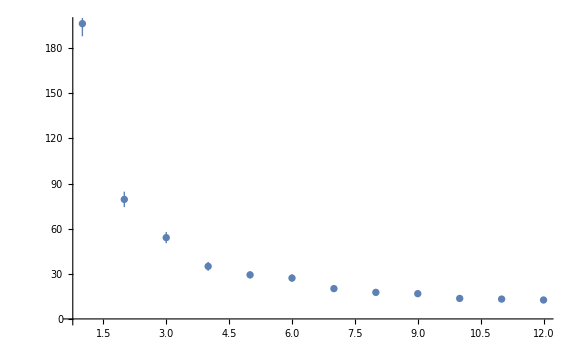

```mathematica
Normal@dsar[
"he","rk",
All
/*
Transpose
/*
Map[Values]
/*
Map[
Interval[MinMax[#]]&
]
/*
Values
/*
(ListPlot[#,PlotRange->All,ImageSize->Large,IntervalMarkers->"Bars"]&),
"d0",
"ndeevs"
/*
Map[Abs[QuantityMagnitude[#]]&]
]
```